(2 (-1+3 λ))/(3 (1+λ))

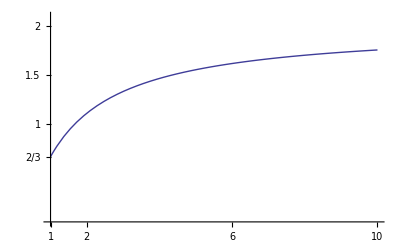

```mathematica
qrbidiag[m_,n_]:=4m n^2-4n^3/3
rbidiag[m_,n_]:=2m n^2+2n^3
ratio[λ_]=Simplify[qrbidiag[m,n]/rbidiag[m,n]/.{m->λ n}]
ratio[1];
Limit[ratio[λ],λ->+Infinity];
λ0=λ/.Solve[ratio[λ]==1,λ][[1]];
Plot[ratio[λ],{λ,1,10},AxesOrigin->{1,0},GridLines->{{λ0},{1,2}},PlotRange->{All,{0,2.1}},Ticks->{{1,λ0,2,4,6,8,10},{ratio[1],1,1.5,2}}]
```